```mathematica
(* Jackson Problem 3.12 *)
(* ----------------------- *)
```

```mathematica
(* Integral for part a *)
(* ----------------------- *)
Integrate[BesselJ[0,k*r]*r,{r,0,a}]
```

(a BesselJ[1,a k])/k

```mathematica
(* Integral for part b *)
(* ----------------------- *)
Integrate[BesselJ[1,k*a]*Exp[-k*z],{k,0,Infinity},Assumptions->{z>0,a>0}]
```

(1-z/(√(a^2+z^2)))/a

```mathematica
(* Integral for part c *)
(* ----------------------- *)
Integrate[BesselJ[0,k*a]*BesselJ[1,k*a]*Exp[-k*z],{k,0,Infinity},Assumptions->{a>0,z>0}]
```

(π-2 EllipticK[-(4 a^2)/z^2])/(2 a π)

```mathematica
(* compare to Jackson's result *)
(* -------------------------------- *)
f1[z_]:=1-2/Pi*EllipticK[-4/z^2]
kk[z_]:=2/Sqrt[z^2+4]
f2[z_]:=1-z*kk[z]/Pi*EllipticK[kk[z]]
```

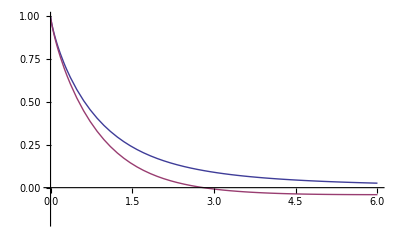

```mathematica
Plot[{f1[z],f2[z]},{z,0,6},PlotRange->{-0.2,1}]
```

```mathematica
(* Plot potential for a=1 *)
(* -------------------------- *)
phi[rho_,z_]:=NIntegrate[BesselJ[1,k]*BesselJ[0,k*rho]*Exp[-k*z],{k,0,25}]
```

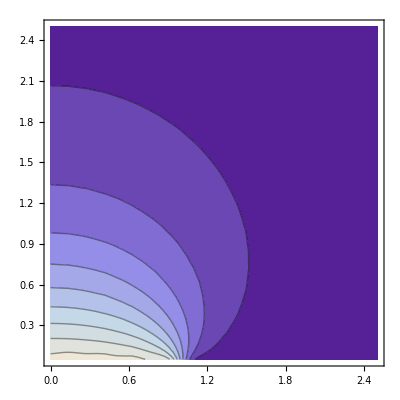

```mathematica
ContourPlot[phi[x,y],{x,0,2.5},{y,0.05,2.5},PlotPoints->10,PlotRange->{0,1}]
```

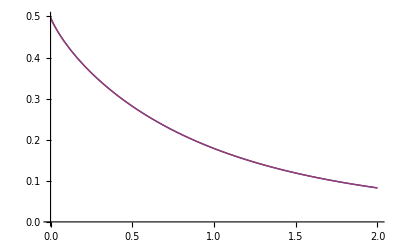

```mathematica
(* agrees with my result, not with Jackson *)
(* ----------------------------------------------- *)
Plot[{phi[1,z],f1[z]/2},{z,0.0,2},PlotRange->{0,0.5}]
```